# CoP in the XY Model

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Import[NotebookDirectory[]<>"/GaussianOptimization.m"]
```

#### Covariance matrix of ground state of the XY model

```mathematica
Clear[XYft,XYcm,XYcmRes]
XYft[{L_,J_,h_,γ_}]:=XYft[{L,J,h,γ}]=Module[{ϵ,a,b,u,v,cor,part1,part2},
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0; (* This is no really needed for even number of excitations, but would be relevant, if we were to construct eigenstates with odd number of excitations! *)
ϵ[k_]:=ϵ[k]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]:=a[k]=-J Cos[k]-h;
b[k_]:=b[k]=γ J Sin[k];
u[k_]:=u[k]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]:=v[k]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
cor=Table[ⅇ^(ⅈ π (x+1)/L),{x,0,L-1}]//N;
part1=((Table[1/(√L)(Abs[v[(2π k+π)/L]]^2-Abs[u[(2π k+π)/L]]^2//N)ⅇ^(ⅈ 2π k/L),{k,0,L-1}]//Fourier)*cor)//Re;
part2=(((Table[1/(√L)2Im[v[(2π k+π)/L]u[(2π k+π)/L]] ⅇ^(ⅈ 2π k/L),{k,0,L-1}]//Fourier)*cor)//Im);
part1+part2]

XYcm[var_]:=XYcm[var]=Module[{L,ft,ΩBlock},
L=var⟦1⟧;
ft=XYft[var];
ΩBlock=ToeplitzMatrix[ReplacePart[RotateRight[ft,1],1->-Last[ft]],-Reverse[ft]];
ArrayFlatten[{{0.,ΩBlock},{-Transpose[ΩBlock],0.}}]
](* in qqpp basis *)
XYcmRes[var_,{dimA_,dimB_,d_}]:=Module[{L,ind,ΩRes},
L=var⟦1⟧;
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
ΩRes=Table[If[Mod[j-l,L]==0,-Reverse[XYft[var]]⟦1⟧,Sign[j-l]XYft[var]⟦Mod[j-l,L]⟧],{j,ind},{l,ind}];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{0.,ΩRes},{-Transpose[ΩRes],0.}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
] (* in qpqp basis *)
```

## Fermionic Complexity of Purification (CoP)

```mathematica
L=100; (* Total number lattice sites *)
J=2.5;h=2;γ=1; (* XY model parameter*)
dimA1=1; dimB1=3; (* dofs of chosen subystems *)
d=5; (* distance subsystems *)
dimPur=dimA1+dimB1; (* dimensions of the purifying system*)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=XYcmRes[{L,J,h,γ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormΩ[CM0];

JT=GOPurifyStandardJFermion[rlist,dimPur,"qpqp"];
JR=GOTransformΩtoJ[GOΩqpqp[dimA1+dimB1+dimPur],"qpqp","qpqp"]; (* reference state *)

J0=JR;
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; (* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

### 1. Define the problem-specific input arguments

```mathematica
function=GOCoPFerm[JT]; gradient=GOCoPgradFerm[JT];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSONoUN[dimPur]}];
M0List=Table[MatrixExp[RandomReal[{0,0.7},Length[LieBasis]].LieBasis].M0,{i,10}];
geometry=GOGeometryConst[LieBasis,J0,-1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

$Aborted

Reason for termination: Function value tolerance reached

Time taken: 46.3718 seconds

Final value: 1.0434

Number of iterations: 764

Number of total corrections: 0

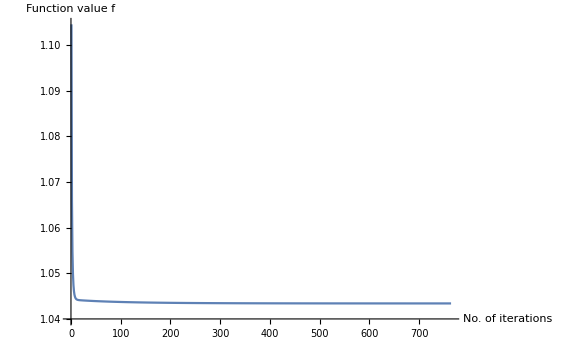

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```

## Calculations

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
XYCoP[L_,J_,h_,γ_,dimA1_,dimB1_,d_]:=Module[{dimPur,CM0,rlist,MTra,JT,JR,J0,M0,function,gradient,ProblemSpecific,LieBasis,M0List,geometry,SystemSpecific},
dimPur=dimA1+dimB1;
CM0=XYcmRes[{L,J,h,γ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormΩ[CM0];
JT=GOPurifyStandardJFermion[rlist,dimPur,"qpqp"];
JR=GOTransformΩtoJ[GOΩqpqp[dimA1+dimB1+dimPur],"qpqp","qpqp"];
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray;
J0=JR;
function=GOCoPFerm[JT]; 
gradient=GOCoPgradFerm[JT];
ProblemSpecific={function,gradient};
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSONoUN[dimPur]}];
M0List=Table[MatrixExp[RandomReal[{0,7/10},Length[LieBasis]].LieBasis].M0,{i,5}];
geometry=GOGeometryConst[LieBasis,J0,-1];
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]]];
```

```mathematica
XYCoPVal[L_,J_,h_,γ_,dimA1_,dimB1_,d_]:=XYCoP[L,J,h,γ,dimA1,dimB1,d]⟦2⟧⟦1,1⟧;
XYCoPTime[L_,J_,h_,γ_,dimA1_,dimB1_,d_]:=XYCoP[L,J,h,γ,dimA1,dimB1,d]⟦1⟧;
```

```mathematica
XYCoPVal[500,1.,1.,1.,10,10,1]
```

1.54939

```mathematica
Export["copF1010XY111N500.txt",Table[{#[[1]],{d,#[[2,1,1]]}}&@XYCoP[500,1.,1.,1.,10,10,d],{d,2,5}]];
```

$Aborted

```mathematica
copF1010XY111N500List={{59659.004,{2,1.5578611041917985}},{664565.86,{3,1.5622954374485298}},{148664.832,{4,1.5650916224459335}},{181959.884,{5,1.567014410433488}}};
```

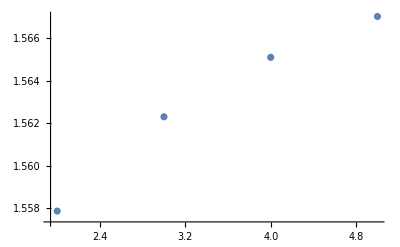

```mathematica
ListPlot[copF1010XY111N500List⟦All,2⟧]
```

```mathematica
Export["copF1212XY111N600.txt",Table[{#[[1]],{d,#[[2,1,1]]}}&@XYCoP[600,1.,1.,1.,12,12,d],{d,2,5}]];
```

```mathematica
copF1212XY111N600List={{1.953314408*^6,{2,1.6884173362400108}},{6.233576484*^6,{3,1.6927295540117568}},{6.819454772*^6,{4,1.695531924028305}},{1.509508332*^6,{5,1.6974343283054703}}};
```

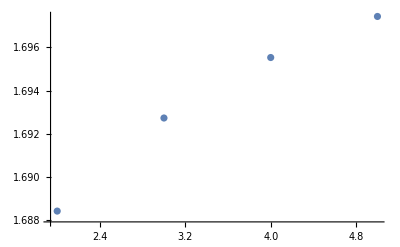

```mathematica
ListPlot[copF1212XY111N600List⟦All,2⟧]
```

```mathematica
Export["copF1414XY111N700.txt",Table[{#[[1]],{d,#[[2,1,1]]}}&@XYCoP[700,1.,1.,1.,14,14,d],{d,2,5}]];
```

```mathematica
copF1414XY111N700List={{1.0440259988*^7,{2,1.8088656919779416}},{9.526854152*^6,{3,1.8130931594482174}},{6.472996148*^6,{4,1.8157248110365583}},{1.385727804*^6,{5,1.8176812918588814}}};
```

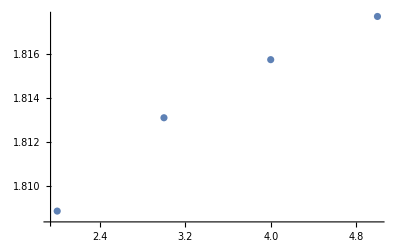

```mathematica
ListPlot[copF1414XY111N700List⟦All,2⟧]
```

## Data and Plots for J=h=γ=1

## L=100 Data

### Data

```mathematica
Table[{d,XYCoPVal[100,1,1,1,1,1,d]},{d,0,98}]
```

{{0,0.576769},{1,0.614313},{2,0.619159},{3,0.620745},{4,0.621461},{5,0.621846},{6,0.622076},{7,0.622225},{8,0.622326},{9,0.622399},{10,0.622452},{11,0.622493},{12,0.622525},{13,0.62255},{14,0.62257},{15,0.622587},{16,0.6226},{17,0.622612},{18,0.622621},{19,0.62263},{20,0.622637},{21,0.622643},{22,0.622648},{23,0.622653},{24,0.622657},{25,0.62266},{26,0.622663},{27,0.622666},{28,0.622669},{29,0.622671},{30,0.622673},{31,0.622675},{32,0.622676},{33,0.622678},{34,0.622679},{35,0.62268},{36,0.622681},{37,0.622682},{38,0.622683},{39,0.622684},{40,0.622684},{41,0.622685},{42,0.622685},{43,0.622686},{44,0.622686},{45,0.622687},{46,0.622687},{47,0.622687},{48,0.622687},{49,0.622687},{50,0.622687},{51,0.622687},{52,0.622687},{53,0.622687},{54,0.622686},{55,0.622686},{56,0.622685},{57,0.622685},{58,0.622684},{59,0.622684},{60,0.622683},{61,0.622682},{62,0.622681},{63,0.62268},{64,0.622679},{65,0.622678},{66,0.622676},{67,0.622675},{68,0.622673},{69,0.622671},{70,0.622669},{71,0.622666},{72,0.622663},{73,0.62266},{74,0.622657},{75,0.622653},{76,0.622648},{77,0.622643},{78,0.622637},{79,0.62263},{80,0.622621},{81,0.622612},{82,0.6226},{83,0.622587},{84,0.62257},{85,0.62255},{86,0.622525},{87,0.622493},{88,0.622452},{89,0.622399},{90,0.622326},{91,0.622225},{92,0.622076},{93,0.621846},{94,0.621461},{95,0.620745},{96,0.619159},{97,0.614313},{98,0.576769}}

```mathematica
copF11XY111N100Data={{0,0.5767694468081405},{1,0.6143134171462082},{2,0.6191591636196478},{3,0.6207452146576419},{4,0.6214612991703838},{5,0.6218456127071338},{6,0.6220757663593777},{7,0.6222245039620508},{8,0.6223261846997175},{9,0.6223987623577489},{10,0.6224523718186856},{11,0.6224930858660278},{12,0.6225247341887997},{13,0.622549808574127},{14,0.6225700171631628},{15,0.6225865292646349},{16,0.6226001957747396},{17,0.6226116288742541},{18,0.6226212832131975},{19,0.6226295067191421},{20,0.6226365688643215},{21,0.6226426644950797},{22,0.6226479662537083},{23,0.6226525978645209},{24,0.6226566665503273},{25,0.6226602535340946},{26,0.6226634251238492},{27,0.622666245268564},{28,0.622668752894536},{29,0.6226709966899688},{30,0.6226729986850257},{31,0.6226747917752065},{32,0.6226763973392132},{33,0.6226778415050779},{34,0.622679134591386},{35,0.6226802938921497},{36,0.6226813276465348},{37,0.6226822551695452},{38,0.6226830805487884},{39,0.6226838051235155},{40,0.6226844474368618},{41,0.6226850117981655},{42,0.6226854943497697},{43,0.6226859048466882},{44,0.6226862505943453},{45,0.6226865279598292},{46,0.6226867404013483},{47,0.6226868898656197},{48,0.6226869776781871},{49,0.6226870104609088},{50,0.6226869798956252},{51,0.6226868903909373},{52,0.6226867376008681},{53,0.622686524622531},{54,0.6226862495461872},{55,0.6226859054998642},{56,0.6226854963921654},{57,0.6226850102271597},{58,0.6226844499519437},{59,0.6226838069195713},{60,0.622683075958935},{61,0.6226822555261832},{62,0.6226813288550624},{63,0.6226802921722281},{64,0.6226791315374846},{65,0.6226778397568857},{66,0.6226764007214275},{67,0.6226747894845517},{68,0.6226729959071601},{69,0.6226709947581879},{70,0.6226687574984318},{71,0.6226662452218776},{72,0.6226634283573298},{73,0.6226602504506914},{74,0.6226566635825097},{75,0.6226526009835713},{76,0.6226479634301986},{77,0.6226426652670956},{78,0.622636565803812},{79,0.6226295102347021},{80,0.6226212820567663},{81,0.622611630870636},{82,0.6226001994934321},{83,0.6225865295453445},{84,0.6225700161019788},{85,0.6225498101468407},{86,0.6225247339802822},{87,0.622493087833981},{88,0.6224523686989145},{89,0.622398764115068},{90,0.622326184775981},{91,0.6222245045083343},{92,0.6220757680722548},{93,0.6218456097449157},{94,0.6214612979981112},{95,0.6207452146095641},{96,0.6191591650500021},{97,0.6143134188210567},{98,0.5767694461272869}};
```

```mathematica
InvcopF11XY111N100Data={1/(#⟦1⟧),#⟦2⟧}&/@copF11XY111N100Data;
```

```mathematica
InvcopF11XY111N100Data={{0,0.5767694468081405},{1,0.6143134171462082},{1/2,0.6191591636196478},{1/3,0.6207452146576419},{1/4,0.6214612991703838},{1/5,0.6218456127071338},{1/6,0.6220757663593777},{1/7,0.6222245039620508},{1/8,0.6223261846997175},{1/9,0.6223987623577489},{1/10,0.6224523718186856},{1/11,0.6224930858660278},{1/12,0.6225247341887997},{1/13,0.622549808574127},{1/14,0.6225700171631628},{1/15,0.6225865292646349},{1/16,0.6226001957747396},{1/17,0.6226116288742541},{1/18,0.6226212832131975},{1/19,0.6226295067191421},{1/20,0.6226365688643215},{1/21,0.6226426644950797},{1/22,0.6226479662537083},{1/23,0.6226525978645209},{1/24,0.6226566665503273},{1/25,0.6226602535340946},{1/26,0.6226634251238492},{1/27,0.622666245268564},{1/28,0.622668752894536},{1/29,0.6226709966899688},{1/30,0.6226729986850257},{1/31,0.6226747917752065},{1/32,0.6226763973392132},{1/33,0.6226778415050779},{1/34,0.622679134591386},{1/35,0.6226802938921497},{1/36,0.6226813276465348},{1/37,0.6226822551695452},{1/38,0.6226830805487884},{1/39,0.6226838051235155},{1/40,0.6226844474368618},{1/41,0.6226850117981655},{1/42,0.6226854943497697},{1/43,0.6226859048466882},{1/44,0.6226862505943453},{1/45,0.6226865279598292},{1/46,0.6226867404013483},{1/47,0.6226868898656197},{1/48,0.6226869776781871},{1/49,0.6226870104609088},{1/50,0.6226869798956252},{1/51,0.6226868903909373},{1/52,0.6226867376008681},{1/53,0.622686524622531},{1/54,0.6226862495461872},{1/55,0.6226859054998642},{1/56,0.6226854963921654},{1/57,0.6226850102271597},{1/58,0.6226844499519437},{1/59,0.6226838069195713},{1/60,0.622683075958935},{1/61,0.6226822555261832},{1/62,0.6226813288550624},{1/63,0.6226802921722281},{1/64,0.6226791315374846},{1/65,0.6226778397568857},{1/66,0.6226764007214275},{1/67,0.6226747894845517},{1/68,0.6226729959071601},{1/69,0.6226709947581879},{1/70,0.6226687574984318},{1/71,0.6226662452218776},{1/72,0.6226634283573298},{1/73,0.6226602504506914},{1/74,0.6226566635825097},{1/75,0.6226526009835713},{1/76,0.6226479634301986},{1/77,0.6226426652670956},{1/78,0.622636565803812},{1/79,0.6226295102347021},{1/80,0.6226212820567663},{1/81,0.622611630870636},{1/82,0.6226001994934321},{1/83,0.6225865295453445},{1/84,0.6225700161019788},{1/85,0.6225498101468407},{1/86,0.6225247339802822},{1/87,0.622493087833981},{1/88,0.6224523686989145},{1/89,0.622398764115068},{1/90,0.622326184775981},{1/91,0.6222245045083343},{1/92,0.6220757680722548},{1/93,0.6218456097449157},{1/94,0.6214612979981112},{1/95,0.6207452146095641},{1/96,0.6191591650500021},{1/97,0.6143134188210567},{1/98,0.5767694461272869}};
```

### Plots

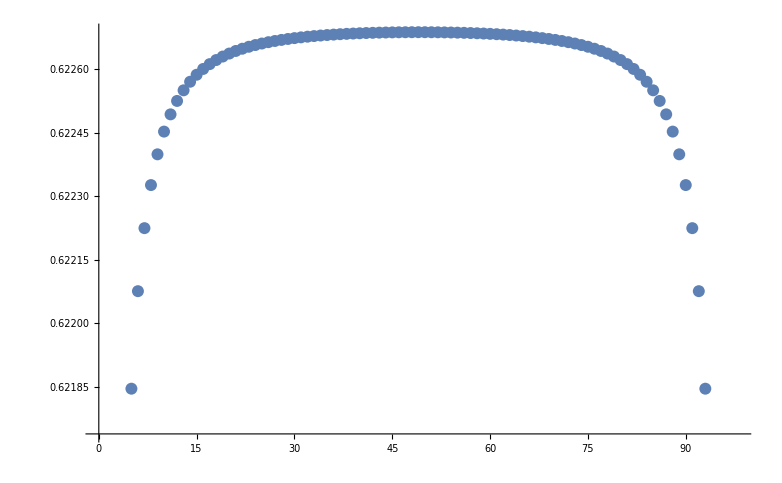

```mathematica
ListPlot[copF11XY111N100Data]
```

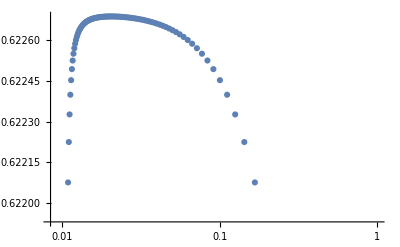

```mathematica
ListLogLinearPlot[InvcopF11XY111N100Data]
```

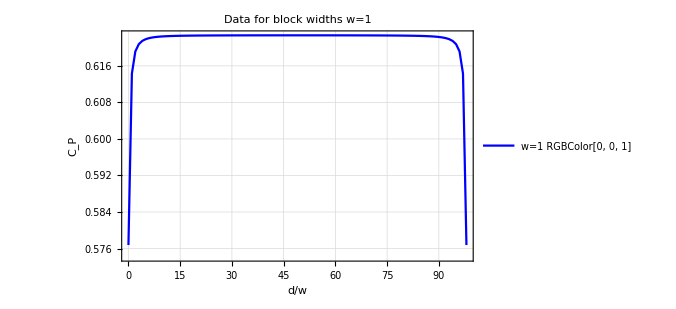

```mathematica
Show[ListPlot[copF11XY111N100Data,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1",PlotLegends->{Blue"w=1"}]]
```

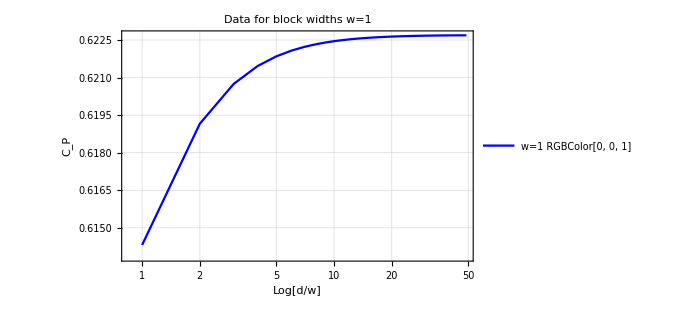

```mathematica
Show[ListLogLinearPlot[copF11XY111N100Data⟦1;;50⟧,PlotTheme->"Detailed",PlotStyle->{Blue},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"Log[d/w]", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1",PlotLegends->{Blue"w=1"}]]
```

## L=200 Data

### Data

```mathematica
Table[{d,XYCoPVal[200,1,1,1,2,2,d]},{d,0,96}]
```

{{0,0.75877},{1,0.800876},{2,0.80835},{3,0.811236},{4,0.812685},{5,0.813521},{6,0.814051},{7,0.814408},{8,0.81466},{9,0.814845},{10,0.814985},{11,0.815093},{12,0.815179},{13,0.815248},{14,0.815304},{15,0.815351},{16,0.81539},{17,0.815423},{18,0.815451},{19,0.815475},{20,0.815496},{21,0.815514},{22,0.81553},{23,0.815544},{24,0.815556},{25,0.815567},{26,0.815577},{27,0.815586},{28,0.815594},{29,0.815601},{30,0.815608},{31,0.815614},{32,0.81562},{33,0.815625},{34,0.815629},{35,0.815633},{36,0.815637},{37,0.815641},{38,0.815644},{39,0.815647},{40,0.81565},{41,0.815653},{42,0.815655},{43,0.815657},{44,0.81566},{45,0.815662},{46,0.815663},{47,0.815665},{48,0.815667},{49,0.815668},{50,0.81567},{51,0.815671},{52,0.815672},{53,0.815674},{54,0.815675},{55,0.815676},{56,0.815677},{57,0.815678},{58,0.815679},{59,0.81568},{60,0.81568},{61,0.815681},{62,0.815682},{63,0.815683},{64,0.815683},{65,0.815684},{66,0.815685},{67,0.815685},{68,0.815686},{69,0.815686},{70,0.815687},{71,0.815687},{72,0.815687},{73,0.815688},{74,0.815688},{75,0.815689},{76,0.815689},{77,0.815689},{78,0.81569},{79,0.81569},{80,0.81569},{81,0.81569},{82,0.815691},{83,0.815691},{84,0.815691},{85,0.815691},{86,0.815691},{87,0.815691},{88,0.815692},{89,0.815692},{90,0.815692},{91,0.815692},{92,0.815692},{93,0.815692},{94,0.815692},{95,0.815692},{96,0.815692}}

```mathematica
copF22XY111N200Data={{0,0.7587704389714912},{1,0.8008759852191335},{2,0.8083499212753943},{3,0.811236364349404},{4,0.812684591257634},{5,0.8135213720758475},{6,0.8140506793498281},{7,0.8144075353619691},{8,0.8146598508818534},{9,0.8148449822189137},{10,0.8149849235041394},{11,0.8150933112026724},{12,0.8151789844404821},{13,0.8152479035766854},{14,0.8153041709171356},{15,0.8153507050901178},{16,0.8153896332393892},{17,0.815422526228668},{18,0.8154505839679702},{19,0.8154746951730883},{20,0.815495571864415},{21,0.8155137738436987},{22,0.8155297315940153},{23,0.8155438004176782},{24,0.8155562631103207},{25,0.81556736655751},{26,0.8155772840126227},{27,0.8155862001936045},{28,0.8155942253689697},{29,0.8156014771133435},{30,0.8156080654780721},{31,0.8156140531390094},{32,0.8156195152130593},{33,0.8156245137587503},{34,0.8156290950764228},{35,0.8156333040719436},{36,0.815637177240131},{37,0.8156407582122798},{38,0.815644070820225},{39,0.8156471357470764},{40,0.815649977191042},{41,0.8156526267151393},{42,0.8156550902423298},{43,0.8156573862541272},{44,0.8156595217076582},{45,0.8156615305116709},{46,0.8156634050986394},{47,0.8156651648969596},{48,0.8156668090526117},{49,0.8156683607914612},{50,0.8156698137148977},{51,0.8156711825951386},{52,0.8156724745046616},{53,0.8156736883838623},{54,0.815674829254766},{55,0.8156759141870034},{56,0.8156769336323403},{57,0.8156778944343119},{58,0.8156788068691857},{59,0.8156796679920381},{60,0.8156804829231337},{61,0.815681252148889},{62,0.8156819878965196},{63,0.8156826821362252},{64,0.8156833361348339},{65,0.8156839485029801},{66,0.8156845412331666},{67,0.815685095560397},{68,0.8156856188384645},{69,0.8156861173244485},{70,0.8156865962188715},{71,0.8156870362547374},{72,0.8156874616820188},{73,0.8156878619616429},{74,0.8156882346544714},{75,0.8156885849041375},{76,0.8156889267086123},{77,0.8156892429139476},{78,0.8156895359933728},{79,0.8156898125013794},{80,0.8156900763643358},{81,0.8156903170943757},{82,0.8156905427788451},{83,0.8156907512765678},{84,0.8156909455414333},{85,0.8156911302416007},{86,0.8156912892724049},{87,0.8156914387755858},{88,0.8156915758620025},{89,0.815691697521568},{90,0.8156918118522223},{91,0.8156919051755428},{92,0.8156919881024849},{93,0.815692061606516},{94,0.8156921175249152},{95,0.8156921608989552},{96,0.8156921866975283}};
```

```mathematica
copF22XY111N200DataReg={#⟦1⟧/2,#⟦2⟧}&/@copF22XY111N200Data;
```

### Plots

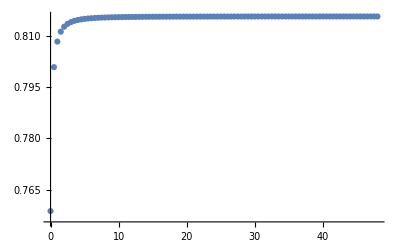

```mathematica
ListPlot[copF22XY111N200DataReg,PlotRange->All]
```

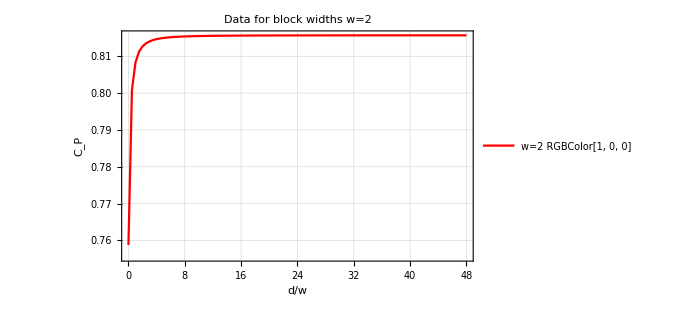

```mathematica
Show[ListPlot[copF22XY111N200DataReg,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=2",PlotLegends->{Red"w=2"}]]
```

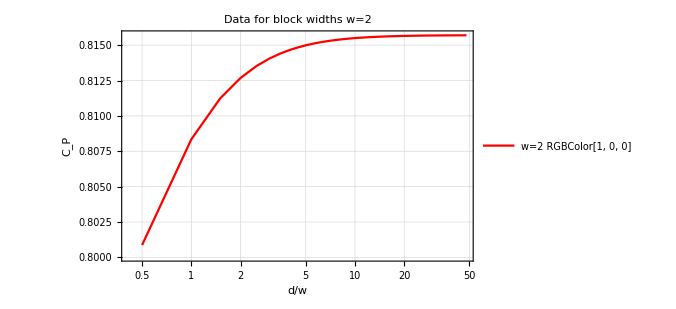

```mathematica
Show[ListLogLinearPlot[copF22XY111N200DataReg,PlotTheme->"Detailed",PlotStyle->{Red},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=2",PlotLegends->{Red"w=2"}]]
```

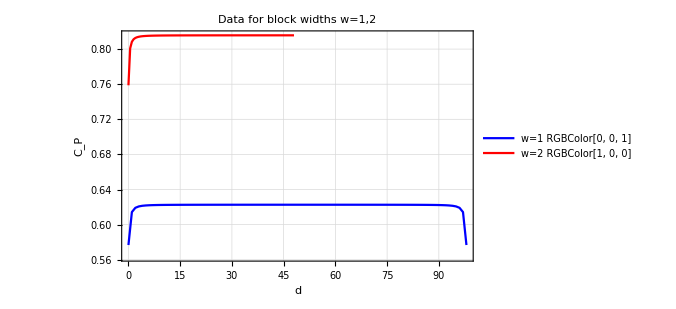

```mathematica
Show[ListPlot[{copF11XY111N100Data,copF22XY111N200DataReg},PlotTheme->"Detailed",PlotStyle->{Blue,Red},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2",PlotLegends->{Blue"w=1",Red"w=2"}]]
```

## L=300 Data

### Data

```mathematica
Table[{d,XYCoPVal[300,1,1,1,3,3,d]},{d,0,60}]
```

{{0,0.896304},{1,0.937622},{2,0.946158},{3,0.949794},{4,0.951742},{5,0.952924},{6,0.953701},{7,0.954241},{8,0.954632},{9,0.954925},{10,0.955151},{11,0.955328},{12,0.95547},{13,0.955586},{14,0.955681},{15,0.955761},{16,0.955828},{17,0.955885},{18,0.955935},{19,0.955977},{20,0.956014},{21,0.956047},{22,0.956075},{23,0.9561},{24,0.956123},{25,0.956143},{26,0.956161},{27,0.956177},{28,0.956192},{29,0.956205},{30,0.956218},{31,0.956229},{32,0.956239},{33,0.956248},{34,0.956257},{35,0.956265},{36,0.956272},{37,0.956279},{38,0.956285},{39,0.956291},{40,0.956296},{41,0.956301},{42,0.956306},{43,0.95631},{44,0.956314},{45,0.956318},{46,0.956322},{47,0.956325},{48,0.956328},{49,0.956331},{50,0.956334},{51,0.956337},{52,0.956339},{53,0.956342},{54,0.956344},{55,0.956346},{56,0.956348},{57,0.95635},{58,0.956352},{59,0.956354},{60,0.956356}}

```mathematica
copF33XY111N300Data1={{0,0.8963039023975892},{1,0.9376216642087778},{2,0.9461578866403998},{3,0.9497936489813371},{4,0.951741847268669},{5,0.9529239509355513},{6,0.9537006755768986},{7,0.9542405268066726},{8,0.9546318991672683},{9,0.9549251247461356},{10,0.9551507485426659},{11,0.9553281817841748},{12,0.9554703289692211},{13,0.9555860006778314},{14,0.9556814200017554},{15,0.9557610771794657},{16,0.9558282759673897},{17,0.9558854806481961},{18,0.9559346010797077},{19,0.9559770856284213},{20,0.9560140789673889},{21,0.9560465036420978},{22,0.956075066710426},{23,0.9561003721685322},{24,0.956122889042888},{25,0.9561430211445004},{26,0.9561610844146586},{27,0.956177368320054},{28,0.9561920782302603},{29,0.9562054278529479},{30,0.9562175745822596},{31,0.9562286564717627},{32,0.9562387986006268},{33,0.9562480941005098},{34,0.9562566544452779},{35,0.9562645315482726},{36,0.9562718091392673},{37,0.9562785508524647},{38,0.9562848020429527},{39,0.9562906052238648},{40,0.9562959965606306},{41,0.9563010381304583},{42,0.9563057341273457},{43,0.9563101247856329},{44,0.9563142387801828},{45,0.9563180997194222},{46,0.9563217247514867},{47,0.9563251237913875},{48,0.9563283336797579},{49,0.9563313499814335},{50,0.95633420071583},{51,0.9563368865859343},{52,0.9563394270493433},{53,0.9563418348177118},{54,0.9563441164092851},{55,0.9563462733296914},{56,0.9563483208735897},{57,0.9563502692998749},{58,0.9563521211509647},{59,0.9563538770651594},{60,0.956355552315695}};
```

```mathematica
copF33XY111N300Data1Reg={#⟦1⟧/3,#⟦2⟧}&/@copF33XY111N300Data1;
```

```mathematica
InvcopcopF33XY111N300Data1Reg={1/#⟦1⟧,#⟦2⟧}&/@copF33XY111N300Data1Reg;
```

```mathematica
InvcopcopF33XY111N300Data1Reg={{0,0.8963039023975892},{3,0.9376216642087778},{3/2,0.9461578866403998},{1,0.9497936489813371},{3/4,0.951741847268669},{3/5,0.9529239509355513},{1/2,0.9537006755768986},{3/7,0.9542405268066726},{3/8,0.9546318991672683},{1/3,0.9549251247461356},{3/10,0.9551507485426659},{3/11,0.9553281817841748},{1/4,0.9554703289692211},{3/13,0.9555860006778314},{3/14,0.9556814200017554},{1/5,0.9557610771794657},{3/16,0.9558282759673897},{3/17,0.9558854806481961},{1/6,0.9559346010797077},{3/19,0.9559770856284213},{3/20,0.9560140789673889},{1/7,0.9560465036420978},{3/22,0.956075066710426},{3/23,0.9561003721685322},{1/8,0.956122889042888},{3/25,0.9561430211445004},{3/26,0.9561610844146586},{1/9,0.956177368320054},{3/28,0.9561920782302603},{3/29,0.9562054278529479},{1/10,0.9562175745822596},{3/31,0.9562286564717627},{3/32,0.9562387986006268},{1/11,0.9562480941005098},{3/34,0.9562566544452779},{3/35,0.9562645315482726},{1/12,0.9562718091392673},{3/37,0.9562785508524647},{3/38,0.9562848020429527},{1/13,0.9562906052238648},{3/40,0.9562959965606306},{3/41,0.9563010381304583},{1/14,0.9563057341273457},{3/43,0.9563101247856329},{3/44,0.9563142387801828},{1/15,0.9563180997194222},{3/46,0.9563217247514867},{3/47,0.9563251237913875},{1/16,0.9563283336797579},{3/49,0.9563313499814335},{3/50,0.95633420071583},{1/17,0.9563368865859343},{3/52,0.9563394270493433},{3/53,0.9563418348177118},{1/18,0.9563441164092851},{3/55,0.9563462733296914},{3/56,0.9563483208735897},{1/19,0.9563502692998749},{3/58,0.9563521211509647},{3/59,0.9563538770651594},{1/20,0.956355552315695}};
```

```mathematica
Table[{d,XYCoPVal[300,1,1,1,3,3,d]},{d,60,200,2}]
```

$Aborted

### Plots

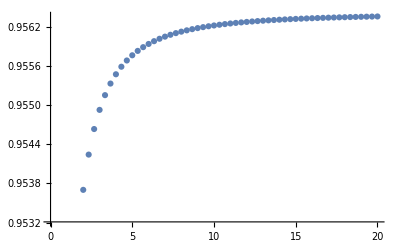

```mathematica
ListPlot[copF33XY111N300Data1Reg]
```

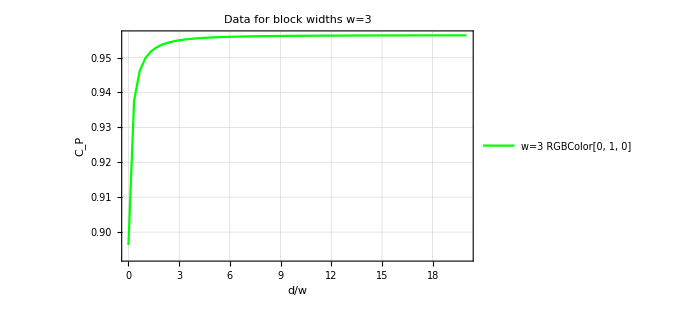

```mathematica
Show[ListPlot[copF33XY111N300Data1Reg,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=3",PlotLegends->{Green"w=3"}]]
```

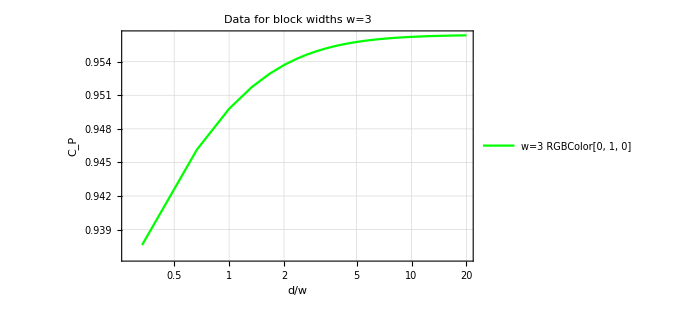

```mathematica
Show[ListLogLinearPlot[copF33XY111N300Data1Reg,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=3",PlotLegends->{Green"w=3"}]]
```

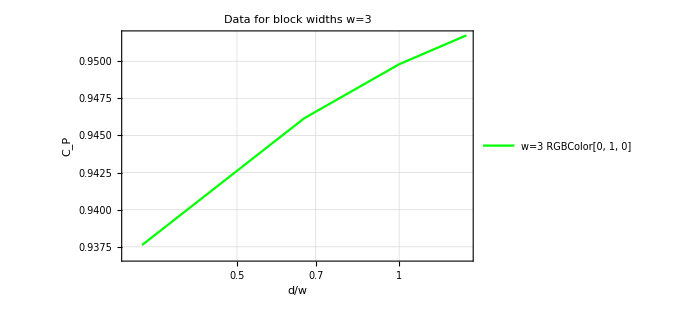

```mathematica
Show[ListLogLinearPlot[copF33XY111N300Data1Reg⟦1;;5⟧,PlotTheme->"Detailed",PlotStyle->{Green},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=3",PlotLegends->{Green"w=3"}]]
```

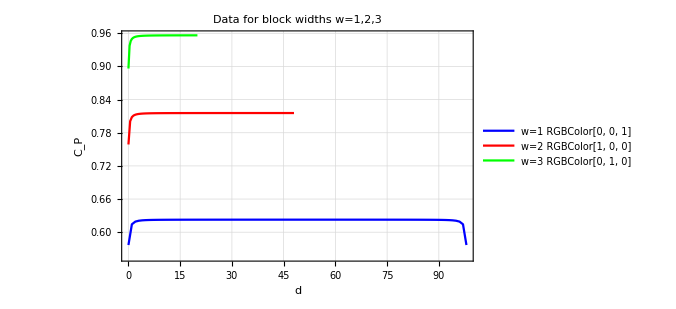

```mathematica
Show[ListPlot[{copF11XY111N100Data,copF22XY111N200DataReg,copF33XY111N300Data1Reg},PlotTheme->"Detailed",PlotStyle->{Blue,Red,Green},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=1,2,3",PlotLegends->{Blue"w=1",Red"w=2",Green"w=3"}]]
```

## L=500 Data

### Data

```mathematica
FullcopF1010XY111N500Data={{59659.004,{2,1.5578611041917985}},{664565.86,{3,1.5622954374485298}},{148664.832,{4,1.5650916224459335}},{181959.884,{5,1.567014410433488}}};
```

```mathematica
copF1010XY111N500Data={{2,1.5578611041917985},{3,1.5622954374485298},{4,1.5650916224459335},{5,1.567014410433488}};
```

```mathematica
copF1010XY111N500Data
```

{{2,1.55786},{3,1.5623},{4,1.56509},{5,1.56701}}

```mathematica
copF1010XY111N500DataReg={#⟦1⟧/10,#⟦2⟧}&/@copF1010XY111N500Data;
```

```mathematica
N[copF1010XY111N500DataReg]
```

{{0.2,1.55786},{0.3,1.5623},{0.4,1.56509},{0.5,1.56701}}

```mathematica
InvcopF1010XY111N500DataReg={1/#⟦1⟧,#⟦2⟧}&/@copF1010XY111N500DataReg;
```

### Plots

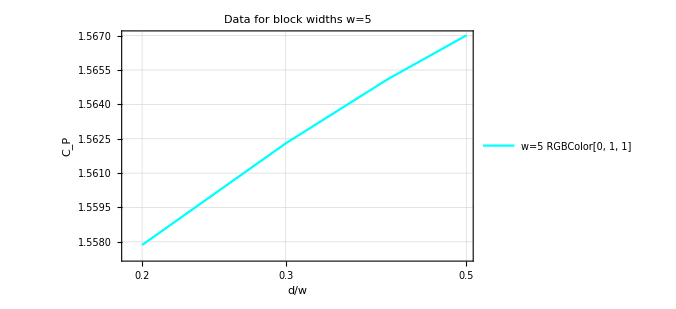

```mathematica
Show[ListLogLinearPlot[copF1010XY111N500DataReg,PlotTheme->"Detailed",PlotStyle->{Cyan},Joined->True,PlotRange->All,PlotMarkers->None,Axes->True,Frame->True,PlotStyle->Thick,
FrameLabel->{"d/w", "C_P"},FrameStyle->Directive[FontFamily->"Times",FontSize->25,GrayLevel[.1]],LabelStyle ->Directive[FontFamily->"Times",FontSize->20,GrayLevel[.1]],ImageSize->500,PlotLabel->"Data for block widths w=5",PlotLegends->{Cyan"w=5"}]]
```

```mathematica
Normal[NonlinearModelFit[copF1010XY111N500DataReg,a Log[x]+b,{a,b},x]]
```

1.57416+0.0100328 Log[x]

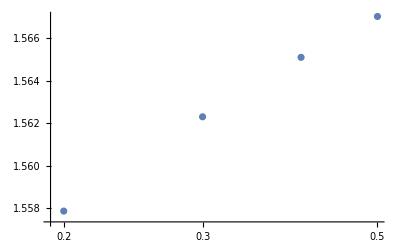

```mathematica
ListLogLinearPlot[copF1010XY111N500DataReg]
```

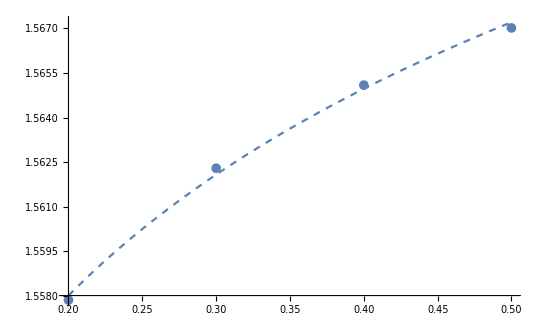

```mathematica
Show[{Plot[1.57415898029597+0.010032752731177026 Log[x],{x,0.2,0.5},PlotStyle->Dashed],ListPlot[copF1010XY111N500DataReg,Joined->False,PlotStyle->Thick]},PlotRange-> All]
```

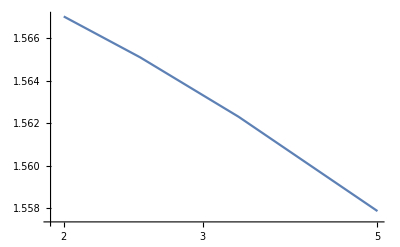

```mathematica
ListLogLinearPlot[InvcopF1010XY111N500DataReg,Joined->True]
```

## L=600 Data